```mathematica
SetDirectory[NotebookDirectory[]<>"Simulation/Simulation/bin/Release"]
```

D:\work\TU\FitzHugh-Nagumo Heterogenous Networks\Simulation\Simulation\bin\Release

```mathematica
Set[#,"--"<>ToString@#]&/@{
NodeCount,
CouplingRadius,
CouplingStrength,
TimeScale,
DiffusionConstant,
DeltaTime,
WarmupTime,
MeasurementInterval,
MaximumTime,
DelayTime,
Seed,
BifurcationParameterMean,
BifurcationParameterVariance
};
Set[#,ToString@#]&/@{
Config,
Trajectory
};
```

```mathematica
RunCommand[args__]:=RunProcess[{"Simulation.exe",args},"StandardOutput"];
GetTrajectory[guid_,n_]:=BinaryReadList["./Data/"<>guid<>"/data.bin",ConstantArray["Real64",n]];
```

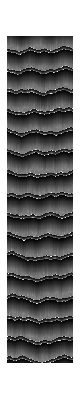

```mathematica
With[{guid=RunCommand[NodeCount,100,Trajectory]},
With[{traj=GetTrajectory[guid,100]},
ArrayPlot@traj
]]
```